# Проектирование оконных функций, суммирующихся в единицу с заданным уровнем перекрытия

Существует ряд задач, в которых длительный по времени сигнал разбивается на сегменты, каждый из которых обрабатывается по отдельности. В частности, такой подход используется для анализа сигнала с помощью оконного преобразования Фурье, или наоборот, при синтезе; а также при спектральной обработке типа удаление шума, изменение темпа, нелинейной фильтрации и других.

 Сам процесс разбиения математически представляется умножением на некоторую весовую (оконную) функцию со смещением. Для самого простого окна - прямоугольного - это может выглядеть так:

Исходный сигнал:

```mathematica
sig[x_]:=4/3((1-ⅇ^(k-x))/(1-ⅇ^k))Sin[20 x^2]/.k->3
```

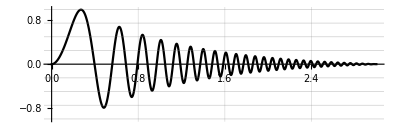

```mathematica
Plot[
sig[x]
,{x,-0.01,3.01},PlotRange->{-1.01,1.01},AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0]}]
```

Разбиения:

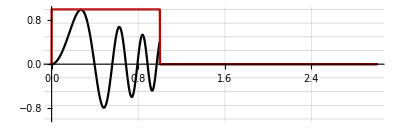

```mathematica
Plot[{
sig[x]DirichletWindow[x-1/2],DirichletWindow[x-1/2]
},{x,-0.01,3.01},PlotRange->{-1.01,1.01},Exclusions->None,AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0],Hue[0, 1, 0.75]}]
```

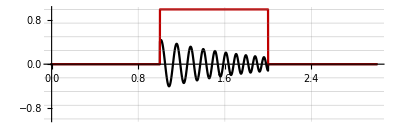

```mathematica
Plot[{
sig[x]DirichletWindow[x-1/2-1],DirichletWindow[x-1/2-1]
},{x,-0.01,3.01},PlotRange->{-1.01,1.01},Exclusions->None,AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0],Hue[0, 1, 0.75]}]
```

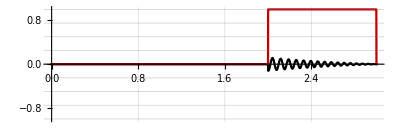

```mathematica
Plot[{
sig[x]DirichletWindow[x-1/2-2],DirichletWindow[x-1/2-2]
},{x,-0.01,3.01},PlotRange->{-1.01,1.01},Exclusions->None,AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0],Hue[0, 1, 0.75]}]
```

Можно восстановить исходный сигнал, просто просуммировав их.

## Подробнее

Однако по ряду причин прямоугольная функция - не самая лучшая оконная функция. При спектральном анализе через (обычно быстрое) дискретное преобразование Фурье анализируемый блок данных как бы “зацикливается”, что приводит к разрыву на краях и искажению спектра:

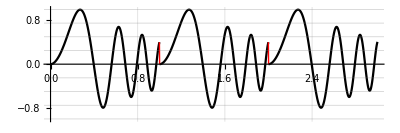

```mathematica
Plot[{
sig[x]DirichletWindow[x-1/2]+
sig[x-1]DirichletWindow[x-1/2-1]+
sig[x-2]DirichletWindow[x-1/2-2]
},{x,0,3},PlotRange->{-1.01,1.01},ExclusionsStyle->Red,AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0]}]
```

Не является оно подходящим и для обратного синтеза - поскольку любое изменение также приведёт к разрывам - например, если мы попробуем реверсировать одну из частей:

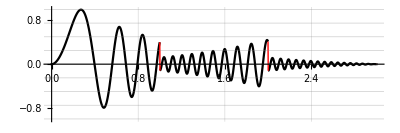

```mathematica
Plot[{
sig[x]DirichletWindow[x-1/2]+
(sig[3-x])DirichletWindow[x-1/2-1]+
sig[x]DirichletWindow[x-1/2-2]

},{x,-0.01,3.01},PlotRange->{-1.01,1.01},ExclusionsStyle->Red,AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0]}]
```

Для устранения этих недостатков используется перекрытие - когда каждое следующее окно захватывает часть данных из предыдущего; а весовое окно, соответственно, плавно спадает к краям.

## Перекрытие в 50%

Наиболее часто для этого используют окно Ханна (известное также под названием «приподнятый косинус») с перекрытием в 50%:

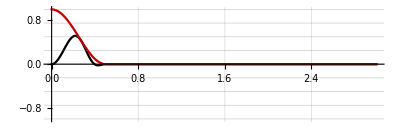

```mathematica
Plot[{
sig[x]HannWindow[x],HannWindow[x]
},{x,-0.01,3.01},PlotRange->{-1.01,1.01},AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0],Hue[0, 1, 0.75]}]
```

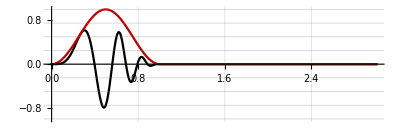

```mathematica
Plot[{
sig[x]HannWindow[x-1/2],HannWindow[x-1/2]
},{x,-0.01,3.01},PlotRange->{-1.01,1.01},AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0],Hue[0, 1, 0.75]}]
```

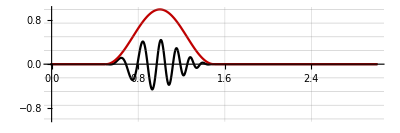

```mathematica
Plot[{
sig[x]HannWindow[x-1],HannWindow[x-1]
},{x,-0.01,3.01},PlotRange->{-1.01,1.01},AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0],Hue[0, 1, 0.75]}]
```

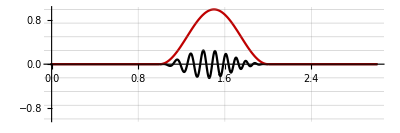

```mathematica
Plot[{
sig[x]HannWindow[x-1-1/2],HannWindow[x-1-1/2]
},{x,-0.01,3.01},PlotRange->{-1.01,1.01},AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0],Hue[0, 1, 0.75]}]
```

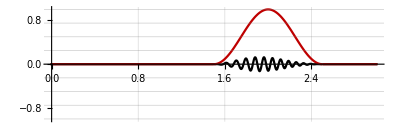

```mathematica
Plot[{
sig[x]HannWindow[x-2],HannWindow[x-2]
},{x,-0.01,3.01},PlotRange->{-1.01,1.01},AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0],Hue[0, 1, 0.75]}]
```

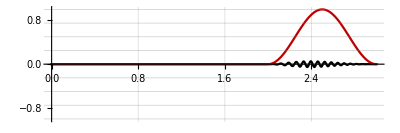

```mathematica
Plot[{
sig[x]HannWindow[x-2-1/2],HannWindow[x-2-1/2]
},{x,-0.01,3.01},PlotRange->{-1.01,1.01},AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0],Hue[0, 1, 0.75]}]
```

За счёт симметричности функции косинуса при сложении они суммируются в единицу:

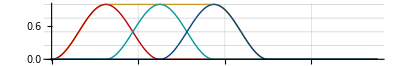

```mathematica
Plot[{
HannWindow[x-1/2]+HannWindow[x-1]+HannWindow[x-3/2],
HannWindow[x-1/2],HannWindow[x-1],HannWindow[x-3/2]
},{x,-0.01,3.01},PlotRange->{0,1},Exclusions->None,PlotStyle->{{Hue[0.12, 1, 0.9],Thick},{Hue[0, 1, 0.75],Thin},{Hue[0.5, 1, 0.6],Thin},{Hue[0.58, 1, 0.5],Thin}},AspectRatio->1/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]}]
```

Теперь при обратном синтезе мы не получим разрывов - но только при условии, что на границах окна значения по-прежнему будут уходить в ноль. Например, при реверсировании одной из частей гладкость не нарушится:

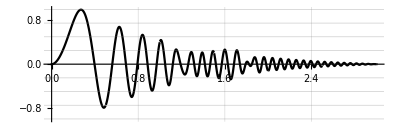

```mathematica
Plot[{
sig[x]HannWindow[x]+
sig[x]HannWindow[x-1/2]+
sig[x]HannWindow[x-2/2]+
sig[3-x]HannWindow[x-3/2]+
sig[x]HannWindow[x-4/2]+
sig[x]HannWindow[x-5/2]+
sig[x]HannWindow[x-6/2]
},{x,-0.01,3.01},PlotRange->{-1.01,1.01},AspectRatio->2/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},PlotStyle->{GrayLevel[0]}]
```

## Обработка с двойным наложением окон

Рассмотрим более подробно алгоритм для обработки сигнала с использованием быстрого преобразования Фурье (FFT):

1) разбиение сигнала на сегменты с наложением окна;
2) прямое FFT;
3) обработка спектра;
4) обратное FFT;
5) повторное наложение окна (поскольку после обратного FFT границы не обязательно будут стыковаться с нулём без разрыва);
6) суммирование результирующих сегментов.

При этом, если обработку спектра не производить, сигнал на выходе должен быть идентичен сигналу на входе (только с неизбежной задержкой во времени).

При использовании окна Ханна перекрытия в 50% уже недостаточно, так как будут возникать провалы:

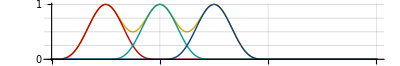

```mathematica
Plot[{
HannWindow[x-1/2]^2+HannWindow[x-1]^2+HannWindow[x-3/2]^2,
HannWindow[x-1/2]^2,HannWindow[x-1]^2,HannWindow[x-3/2]^2
},{x,-0.01,3.01},PlotRange->{0,1},Exclusions->None,PlotStyle->{{Hue[0.12, 1, 0.9],Thick},{Hue[0, 1, 0.75],Thin},{Hue[0.5, 1, 0.6],Thin},{Hue[0.58, 1, 0.5],Thin}},AspectRatio->1/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},Ticks->{{0,0.5,1,1.5,2,2.5,3},{0,0.5,1,1.5}}]
```

Поскольку двойное наложение равносильно возведению в квадрат, то очевидным решением будет использовать корень из окна Ханна, чтобы компенсировать возведение в квадрат:

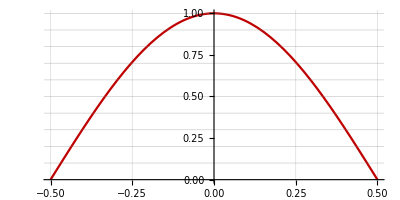

```mathematica
Plot[{
√HannWindow[x]
},{x,-1/2,1/2},AspectRatio->1/2,PlotStyle->Hue[0, 1, 0.75],GridLines->{Table[i,{i,-1,1,0.05}],Table[i,{i,0,1,0.1}]}]
```

В этом случае, правда, окно перестало быть гладким на краях - появился разрыв в первой производной.
[Примечание] Интересно, что в данном случае у нас получилась половина периода синусоиды.

Можно пойти и другим путём - использовать перекрытие в 75%, и тогда окна также будут суммироваться в константу - только уже не в 1, а в 3/2:

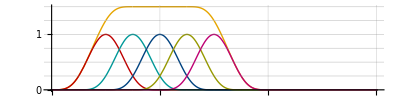

```mathematica
Plot[{
HannWindow[-1/2+x]^2+HannWindow[-3/4+x]^2+HannWindow[-1+x]^2+HannWindow[-5/4+x]^2+HannWindow[-3/2+x]^2,
HannWindow[-1/2+x]^2,HannWindow[-3/4+x]^2,HannWindow[-1+x]^2,HannWindow[-5/4+x]^2,HannWindow[-3/2+x]^2
},{x,-0.01,3.01},PlotRange->{0,1.501},PlotStyle->{{Hue[0.12, 1, 0.9],Thick},{Hue[0, 1, 0.75],Thin},{Hue[0.5, 1, 0.6],Thin},{Hue[0.58, 1, 0.5],Thin},{Hue[0.17, 1, 0.6],Thin},{Hue[0.9, 1, 0.75],Thin}},AspectRatio->1.5/6,GridLines->{Table[i,{i,-3,5,0.125}],Table[i,{i,-1,2,0.25}]},Ticks->{{0,0.5,1,1.5,2,2.5,3},{0,0.5,1,1.5}}]
```

В данном случае нам просто повезло. Если разложить квадрат на сумму - то можно увидеть, что оно представляет собой композицию из двух окон Ханна, но в разных масштабах, что и позволяет выполнять необходимые нам требования:

```mathematica
((cos(2 π x)+1)/2)^2=(cos(2 π x)+1)/2+(cos(4 π x)-1)/8
```

```mathematica
(1/2 (Cos[2 π x]+1))^2=1/2 (Cos[2 π x]+1)+1/8 (Cos[4 π x]-1)
```

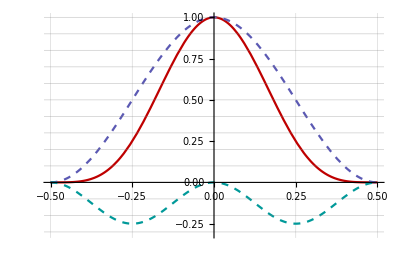

```mathematica
Plot[{
 (1/2+1/2 Cos[2 π x])^2,
1/2+1/2 Cos[2 π x],
1/8 (-1+Cos[4 π x])
},{x,-1/2,1/2},PlotStyle->{Hue[0, 1, 0.75],{Hue[0.67, 0.5, 0.7],Dashed},{Hue[0.5, 1, 0.6],Dashed}},PlotRange->{-.31,1},AspectRatio->1.3/2,GridLines->{Table[i,{i,-1,1,0.05}],Table[i,{i,-1,1,0.1}]}]
```

С другими оконными функциями такой фокус не пройдёт; также далеко не все стандартные оконные функции могут обеспечить суммирование в константу и при 50% перекрытии.

## Идея

Можно  рассматривать окно Ханна не как самостоятельную функцию, а как разницу двух  кусочно-непрерывных функций (подробному рассмотрению которых была посвящена отдельная статья) со смещением. Например, используя следующую функцию

```mathematica
f(x)=Piecewise[{{-1, x≤-1}, {1, x≥1}, {sin((π x)/2), -1<x<1}}]
```

```mathematica
f[x_]:=Piecewise[{{-1, x≤-1}, {1, x≥1}, {Sin[(π x)/2], True}}]
```

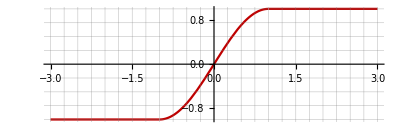

```mathematica
Plot[{
f[x]
},{x,-3,3},AspectRatio->2/6,GridLines->{Table[i,{i,-3,3,0.25}],Table[i,{i,-1,1,0.25}]},PlotStyle->Hue[0, 1, 0.75]]
```

можно записать

```mathematica
f(x+1)-f(x-1)
```

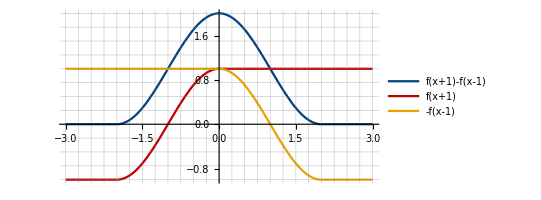

```mathematica
Plot[{
f[x+1]-f[x-1],
f[x+1],
-f[x-1]
},{x,-3,3},AspectRatio->3/6,GridLines->{Table[i,{i,-3,3,0.25}],Table[i,{i,-1,2,0.25}]},PlotLegends->"Expressions",PlotStyle->{Hue[0.58, 1, 0.5],Hue[0, 1, 0.75],Hue[0.12, 1, 0.9]}]
```

Убедиться в их идентичности с окном Ханна можно через приведение к одному масштабу:

```mathematica
f[x+1]-f[x-1]-2HannWindow[x/4]//PiecewiseExpand//Simplify
```

Piecewise[{{-2 Cos[(π x)/4]^2, x==-2||x==2}, {0, True}}]

Рассмотрев компоненты суммы двух таких окон, их способность суммироваться в константу станет более наглядным:

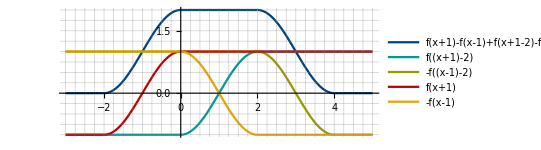

```mathematica
Plot[{
f[x+1]-f[x-1]+f[x+1-2]-f[x-1-2],
f[(x+1)-2],-f[(x-1)-2],
f[x+1],-f[x-1]
},{x,-3,5},AspectRatio->3/8,GridLines->{Table[i,{i,-3,5,0.25}],Table[i,{i,-1,2,0.25}]}, PlotLegends->"Expressions",PlotStyle->{Hue[0.58, 1, 0.5],Hue[0.5, 1, 0.6],Hue[0.17, 1, 0.6],Hue[0, 1, 0.75],Hue[0.12, 1, 0.9],Hue[0.9, 1, 0.75],Hue[0.11, 0.7, 0.75],Hue[0.61, 1, 0.9],Hue[0.08, 1, 1]}]
```

На отрезке [0,2] мы получили взаимную компенсацию при сложении функций -f(x-1) и f((x+1)-2), поскольку  f((x+1)-2)==f (x-1)

Можно выбрать и другое смещение,  с большим перекрытием, например:

```mathematica
f(x+1/2)-f(x-1/2)
```

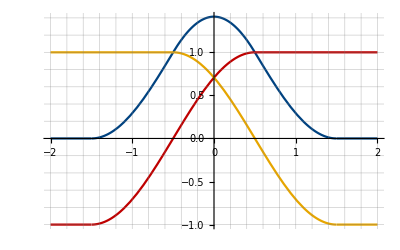

```mathematica
Plot[{
f[x+1/2]-f[x-1/2]
,
f[x+1/2],-f[x-1/2]
},{x,-2,2},AspectRatio->2.5/4,GridLines->{Table[i,{i,-3,3,0.2}],Table[i,{i,-1,1.5,0.2}]},PlotStyle->{Hue[0.58, 1, 0.5],Hue[0, 1, 0.75],Hue[0.12, 1, 0.9]}]
```

И тогда, при смещении с шагом 1/2, они также будут суммироваться в константу:

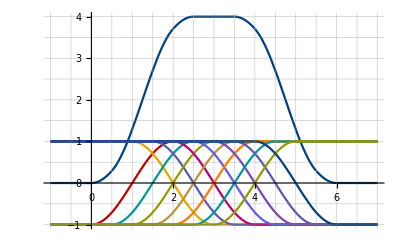

```mathematica
Plot[{
f[x-1]-f[x-2]+
f[x-1-1/2]-f[x-2-1/2]+
f[x-1-2/2]-f[x-2-2/2]+
f[x-1-3/2]-f[x-2-3/2]+
f[x-1-4/2]-f[x-2-4/2]+
f[x-1-5/2]-f[x-2-5/2]+
f[x-1-6/2]-f[x-2-6/2]
,
f[x-1],-f[x-2],
f[x-1-1/2],-f[x-2-1/2],
f[x-1-2/2],-f[x-2-2/2],
f[x-1-3/2],-f[x-2-3/2],
f[x-1-4/2],-f[x-2-4/2],
f[x-1-5/2],-f[x-2-5/2],
f[x-1-6/2],-f[x-2-6/2]
},{x,-1,7},AspectRatio->5/8,GridLines->{Table[i,{i,-1,7,0.5}],Table[i,{i,-1,4,0.5}]},PlotStyle->{Hue[0.58, 1, 0.5],Hue[0, 1, 0.75],Hue[0.12, 1, 0.9],Hue[0.5, 1, 0.6],Hue[0.67, 0.5, 0.7],Hue[0.17, 1, 0.6],Hue[0.9, 1, 0.75],Hue[0.11, 0.7, 0.75],Hue[0.67, 0.6, 0.9],Hue[0.08, 1, 1],Hue[0.75, 0.6, 0.7],Hue[0.5, 1, 0.6],Hue[0.67, 0.5, 0.7],Hue[0.17, 1, 0.6]}]
```

Видно, что если перегруппировать компоненты оконной функции, то получатся всё те же окна Ханна.

Таким образом, используя разные функции ограничения, можно формировать окна необходимой формы.

## Итоговая формула

Теперь осталось только задать масштаб, чтобы области определения и значения не зависели от величины перекрытия. Определив окно в диапазоне [0,1] получим

```mathematica
(f((2 t x)/(t-1)-1)-f((2 t (x-1))/(t-1)+1))/2
```

где f - кусочно-непрерывная функция вида

Piecewise[{{-1, x≤-1}, {1, x≥1}, {g(x), -1<x<1}}]

а g - некоторая интерполирующая функция между точками (-1,1) и (1,1)

В Wolfram Mathematica мы можем определить её следующим образом:

```mathematica
f[x_,g_] := Piecewise[{{-1, x < -1}, {1, x > 1}}, g[x]]
```

А саму обобщённую оконную функцию как

```mathematica
OverlapShape[f_,x_,t_]:=(f[-1+(2 t x)/(-1+t)]-f[1+(2 t (-1+x))/(-1+t)])/2
```

Или, если функция  ограничения задаётся с параметром

```mathematica
OverlapShape[f_,x_,k_,t_]:=(f[-1+(2 t x)/(-1+t), k]-f[1+(2 t (-1+x))/(-1+t),k])/2
```

Параметр t определяет уровень перекрытия - делитель, определяющий шаг, на который необходимо смещать каждое следующее окно, (x_(n+1)=x_n+1/t), и должен быть больше единицы, t>1. 

 Процент перекрытия можно посчитать по формуле

```mathematica
p=(100 (t-1))/t
```

И соответственно наоборот

```mathematica
t=100/(100-p)
```

[примечание] 
При работе с реальными может потребоваться пересчёт уровня перекрытия в зависимости от конкретного размера FFT. Например, при FFT на 2048 точек и уровнем перекрытия 3 получаем шаг 2048/3=682.666..., что на практике, естественно, нереализуемо. Поэтому округлим его до целого, а t пересчитаем как 2048/683=2.998535871156662.
Либо же можно наоборот - использовать размер окна, заведомо делящийся на 3 (скажем, 999), а остаток до необходимого размера для FFT дополнить нулями (25-ю).

Итоговый вид окна будет зависеть как от выбора уровня перекрытия, так и от выбора ограничивающей функции.

Несколько интересных примеров

Здесь мы рассмотрим несколько готовых решений, ради которых всё и затевалось. Для простоты  будем рассматривать просто интерполирующую функцию g(x), без всякой прочей обвязки.

## Полиномиальные окна

Являются наименее вычислительно затратными. Используя ранее выведенную формулу

(2 x n+1/2 1/21-n3/2x^2)/(√π n)

получим полином с заданным количеством нулей на высших производных, обеспечивающих необходимую гладкость окна на краях.

[Первые 10]

```mathematica
Column[Table[(2 x Gamma[1/2+n] Hypergeometric2F1[1/2,1-n,3/2,x^2])/(√π Gamma[n]),{n,1,10}],Center]
```

x
1/2 x (3-x^2)
1/8 x (15-10 x^2+3 x^4)
1/16 x (35-35 x^2+21 x^4-5 x^6)
1/128 x (315-420 x^2+378 x^4-180 x^6+35 x^8)
1/256 x (693-1155 x^2+1386 x^4-990 x^6+385 x^8-63 x^10)
(x (3003-6006 x^2+9009 x^4-8580 x^6+5005 x^8-1638 x^10+231 x^12))/1024
(x (6435-15015 x^2+27027 x^4-32175 x^6+25025 x^8-12285 x^10+3465 x^12-429 x^14))/2048
(x (109395-291720 x^2+612612 x^4-875160 x^6+850850 x^8-556920 x^10+235620 x^12-58344 x^14+6435 x^16))/32768
(x (230945-692835 x^2+1662804 x^4-2771340 x^6+3233230 x^8-2645370 x^10+1492260 x^12-554268 x^14+122265 x^16-12155 x^18))/65536

```mathematica
SoftPolyClip[x_,n_]:=Piecewise[{{-1, x≤-1}, {1, x≥1}, {(2 x Gamma[1/2+n] Hypergeometric2F1[1/2,1-n,3/2,x^2])/(√π Gamma[n]), True}}]
```

С перекрытием в 75% окна с различными значениями n окна будут выглядеть так:

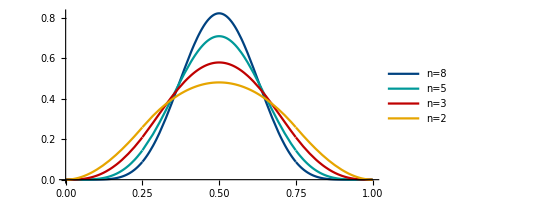

```mathematica
Plot[
Table[
OverlapShape[SoftPolyClip,x,n,4]
,{n,{8,5,3,2}}]//Evaluate
,{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/20}],Table[i,{i,-1,1,1/10}]},PlotLegends->Table["n="<>ToString[n],{n,{8,5,3,2}}],PlotStyle->{Hue[0.58, 1, 0.5],Hue[0.5, 1, 0.6],Hue[0, 1, 0.75],Hue[0.12, 1, 0.9]}]
```

А в случае с извлечением корня - так (при использовании 75% перекрытия):

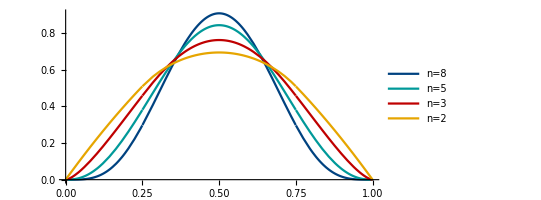

```mathematica
Plot[
Table[
OverlapShape[SoftPolyClip,x,n,4]^(1/2)
,{n,{8,5,3,2}}]//Evaluate
,{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/20}],Table[i,{i,-1,1,1/10}]},PlotLegends->Table["n="<>ToString[n],{n,{8,5,3,2}}],PlotStyle->{Hue[0.58, 1, 0.5],Hue[0.5, 1, 0.6],Hue[0, 1, 0.75],Hue[0.12, 1, 0.9]}]
```

или так (при использовании 50% перекрытия):

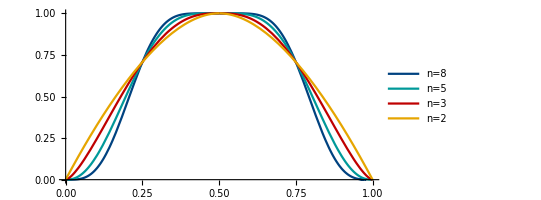

```mathematica
Plot[
Table[
OverlapShape[SoftPolyClip,x,n,2]^(1/2)
,{n,{8,5,3,2}}]//Evaluate
,{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/20}],Table[i,{i,-1,1,1/10}]},PlotLegends->Table["n="<>ToString[n],{n,{8,5,3,2}}],PlotStyle->{Hue[0.58, 1, 0.5],Hue[0.5, 1, 0.6],Hue[0, 1, 0.75],Hue[0.12, 1, 0.9]}]
```

Можно посмотреть на результат и в динамике, вручную изменяя параметры:

```mathematica
Manipulate[Plot[
OverlapShape[SoftPolyClip,x,n,t]
,{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/20}]},PlotStyle->Hue[0.9, 1, 0.75]]
,{{t,4},2,11},{{n,4},1,6,1}]
```

## Максимально гладкое окно

Функция

tanh((k x)/(√(1-x^2)))

интересна тем, что бесконечно дифференцируема и все её производные на краях равны 0 (что можно доказать, рассмотрев её производные исходя из правил дифференцирования - в каждом слагаемом будет обнуляющий его множитель). Это позволяет на её основе строить окна, все производных которых не имеют разрывов:

```mathematica
HyperSoftClip[x_,k_]:=Piecewise[{{-1, x≤-1}, {1, x≥1}, {Tanh[(k x)/(√(1-x^2))], True}}]
```

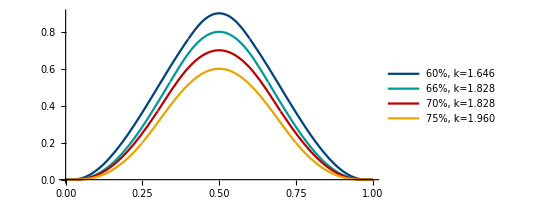

```mathematica
Plot[{
OverlapShape[HyperSoftClip,x,1.6459914282540622,2.5],
OverlapShape[HyperSoftClip,x,1.8278498804990433,50/17],
OverlapShape[HyperSoftClip,x,1.8284300555861006,10/3],
OverlapShape[HyperSoftClip,x,1.9605162869370942,4]
},{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/20}],Table[i,{i,-1,1,1/10}]},PlotLegends->{"60%, k=1.646","66%, k=1.828","70%, k=1.828","75%, k=1.960"},PlotStyle->{Hue[0.58, 1, 0.5],Hue[0.5, 1, 0.6],Hue[0, 1, 0.75],Hue[0.12, 1, 0.9]}]
```

А их вторые производные будут выглядеть так:

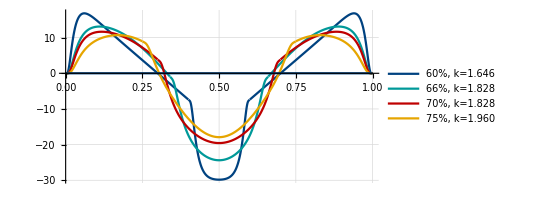

```mathematica
Plot[{
D[OverlapShape[HyperSoftClip,x,1.6459914282540622,2.5],{x,2}]//Evaluate,
D[OverlapShape[HyperSoftClip,x,1.8278498804990433,50/17],{x,2}]//Evaluate,
D[OverlapShape[HyperSoftClip,x,1.8284300555861006,10/3],{x,2}]//Evaluate,
D[OverlapShape[HyperSoftClip,x,1.9605162869370942,4],{x,2}]//Evaluate,
0
},{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->Automatic,PlotLegends->{"60%, k=1.646","66%, k=1.828","70%, k=1.828","75%, k=1.960"},PlotStyle->{Hue[0.58, 1, 0.5],Hue[0.5, 1, 0.6],Hue[0, 1, 0.75],Hue[0.12, 1, 0.9]}]
```

Настройка параметров в динамике:

```mathematica
Manipulate[Plot[
OverlapShape[HyperSoftClip,x,k,t]
,{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/20}]},PlotStyle->Hue[0.9, 1, 0.75]]
,{{t,2.5},1,11},{{k,1.5},1,8}]
```

Вариант с настройкой через высоту окна:

```mathematica
Manipulate[Plot[
OverlapShape[HyperSoftClip,x,1/2 √(1-1/(-1+t)^2) (-1+t) (Log[-1-y]-Log[-1+y]),t]
,{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/20}]},PlotStyle->Hue[0.9, 1, 0.75]]
,{{t,2.5},2,11},{{y,0.8},0.1,1}]
```

## Окно вида “юбочка”

Необходимость такого вида окна вызвана тем, чтобы увеличить разрешение FFT, но снизить влияние эффекта “частотно-временной неопределённости” на высоких частотах за счёт увеличения их концентрации в центре.

Сначала определим  желаемый вид оконной функции - например, следующим образом:

-log(k^2 x^2+1)+log(k^2+1)-(k^2 (1-x^2))/(k^2+1)

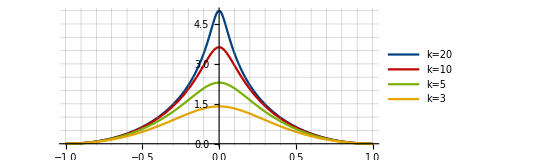

```mathematica
Plot[
Table[-Log[k^2 x^2+1]+Log[k^2+1]-(k^2 (1-x^2))/(k^2+1),{k,{20,10,5,3}}]//Evaluate
,{x,-1,1},PlotRange->{0,5},AspectRatio->2/5,GridLines->{Table[i,{i,-1,1,0.1}],Table[i,{i,0,5,0.5}]},PlotLegends->{"k=20","k=10","k=5","k=3"},PlotStyle->{Hue[0.58, 1, 0.5],Hue[0, 1, 0.75],Hue[0.22, 1, 0.7],Hue[0.12, 1, 0.9],Hue[0.75, 0.6, 0.7]}]
```

Здесь первое слагаемое определяет сам вид функции, второе - обеспечивает пересечение с осью абсцисс, третье (парабола) обнуляет производную на краях для гладкой стыковки; а параметр k определяет “остроту” вершины. В таком виде она ещё не пригодна для использования - сначала из неё нужно получить функцию ограничения посредством интегрирования и масштабирования:

```mathematica
SkirtClip[x_,k_]:=Piecewise[{{-1,x≤-1},{1,x≥1}},Integrate[Log[1+k^2]-Log[1+k^2 x^2]-k^2/(1+k^2)(1-x^2),x]//#/(#/.x->1)&//FullSimplify]//Evaluate
```

```mathematica
SkirtClip//Definition
```

SkirtClip[x_,k_]:=Piecewise[{{-1, x≤-1}, {1, x≥1}, {(k x (6+k^2 (3+x^2))+3 (1+k^2) (-2 ArcTan[k x]+k x (Log[1+k^2]-Log[1+k^2 x^2])))/(6 k+4 k^3-6 (1+k^2) ArcTan[k]), True}}]

Для удобства настройки можно привязать параметр k к уровню перекрытия t - например, таким образом, чтобы 4-ая производная в центре окна была равна 0 - и тогда k будет считаться как √3(t-1) :

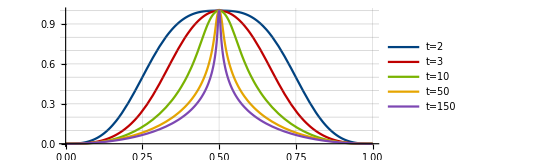

```mathematica
Plot[
Table[OverlapShape[SkirtClip,x,√3 ( t-1),t]/OverlapShape[SkirtClip,1/2,√3 ( t-1),t],{t,{2,3,10,50,150}}]//Evaluate
,{x,0,1},PlotRange->{0,1},AspectRatio->2/5,GridLines->{Table[i,{i,-1,1,0.05}],Table[i,{i,0,1,0.1}]},PlotLegends->{"t=2","t=3","t=10","t=50","t=150"},Axes->{True,False},Exclusions->None,PlotStyle->{Hue[0.58, 1, 0.5],Hue[0, 1, 0.75],Hue[0.22, 1, 0.7],Hue[0.12, 1, 0.9],Hue[0.75, 0.6, 0.7]}]
```

Здесь для наглядности все окна приведены к одному масштабу.

То же окно в динамике:

```mathematica
Manipulate[Plot[
OverlapShape[SkirtClip,x,√3 ( t-1),t]
,{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/20}]},PlotStyle->Hue[0.9, 1, 0.75]]
,{{t,50},1.1,50}]
```

И с независимым контролем параметров:

```mathematica
Manipulate[Plot[
OverlapShape[SkirtClip,x,k,t]
,{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/20}]},PlotStyle->Hue[0.9, 1, 0.75]]
,{{t,50},1.1,100},{{k,50},1.1,100}]
```

## Окно вида “иголка”

Представляет из себя более «агрессивный» вариант предыдущего окна. В качестве основы была выбрана гипербола, из которой путём последовательных трансформаций

```mathematica
1/x->1/(√(x^2))->1/(√(x^2+1))->1/(√(k^2 x^2+1))->((1-x^2)^2)/(√(k^2 x^2+1))
```

```mathematica
Manipulate[
Plot[{
((1-x^2)^2)/(√(1+k^2 x^2))
},{x,-1,1},PlotRange->Full,Evaluated->True,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/10}]},PlotStyle->Hue[0.9, 1, 0.75]]
,{{k,100},1,150}]
```

и использования тех же шагов в виде интегрирования и масштабирования получили формулу

```mathematica
SpikeClip[x_,k_]:=Piecewise[{{-1,x≤-1}, {1,x≥1}},Integrate[((1-x^2)^2)/(√(1+k^2 x^2)),x]//#/(#/.x->1)&//FullSimplify]//Evaluate
```

```mathematica
SpikeClip//Definition
```

SpikeClip[x_,k_]:=Piecewise[{{-1, x≤-1}, {1, x≥1}, {(k x √(1+k^2 x^2) (-3+2 k^2 (-4+x^2))+(3+8 (k^2+k^4)) ArcSinh[k x])/(-3 k √(1+k^2) (1+2 k^2)+(3+8 (k^2+k^4)) ArcSinh[k]), True}}]

Здесь также можно привязать параметр k к уровню перекрытия. Непосредственное решение уравнения 4-ой производной даёт слишком громоздкий результат, поэтому просто сделаем по образу и подобию из решения для предыдущего окна, определив k как  k(t-1), обеспечив таким образом роль параметра k как “тонкая настройка”. При k=2.22 окна будут выглядеть следующим образом:

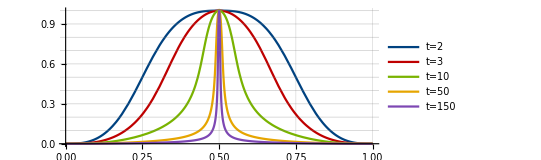

```mathematica
Plot[
Table[OverlapShape[SpikeClip,x,2.22 ( t-1),t]/OverlapShape[SpikeClip,1/2,2.22 ( t-1),t],{t,{2,3,10,50,150}}]//Evaluate
,{x,0,1},PlotRange->{0,1},AspectRatio->2/5,GridLines->{Table[i,{i,-1,1,0.05}],Table[i,{i,0,1,0.1}]},PlotLegends->{"t=2","t=3","t=10","t=50","t=150"},Axes->{True,False},Exclusions->None,PlotStyle->{Hue[0.58, 1, 0.5],Hue[0, 1, 0.75],Hue[0.22, 1, 0.7],Hue[0.12, 1, 0.9],Hue[0.75, 0.6, 0.7]}]
```

В динамике, с зависимым k:

```mathematica
Manipulate[Plot[
OverlapShape[SpikeClip,x,k(t-1),t]
,{x,0,1},PlotRange->All,Exclusions->None,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/10}]},PlotStyle->Hue[0.9, 1, 0.75]]
,{{t,3},2,100},{{k,1.22},0,2}]
```

С независимым k:

```mathematica
Manipulate[Plot[
OverlapShape[SpikeClip,x,k,t]
,{x,0,1},PlotRange->All,Exclusions->None,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/10}]},PlotStyle->Hue[0.9, 1, 0.75]]
,{{t,3},1.1,100},{k,1,50}]
```

## Асимметричное окно

Оконная функция совсем не обязательно должна быть симметричной. Допустим, нам требуется окно с резкой атакой и плавным затуханием. Мы можем получить его по уже знакомой схеме - сначала определить желаемый вид функции, а затем интегрированием получить функцию ограничения. Здесь задача слегка усложняется за счёт того, что из-за асимметрии центр уже не будет проходить через начало координат, поэтому добавляется дополнительный шаг вычислений. Это также приводит к тому, что формулы в результате получаются довольно громоздкими. Для пример рассмотрим простейший вариант - параболу, умноженную на полиномиальное весовое окно:

```mathematica
(1-x)^2 (1-x^10)^2
```

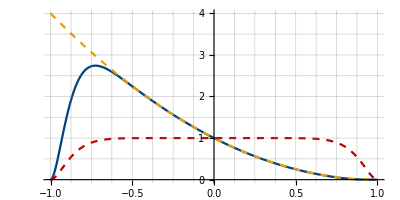

```mathematica
Plot[{
(1-x)^2(1-x^10)^2,
(1-x)^2,(1-x^10)^2
},{x,-1,1},PlotRange->Full,PlotStyle->{Hue[0.58, 1, 0.5],{Hue[0.12, 1, 0.9],Dashed},{Hue[0, 1, 0.75],Dashed}},AspectRatio->2/4,GridLines->{Table[i,{i,-1,1,0.125}],Table[i,{i,0,4,0.5}]}]
```

Здесь степень при x в весовом окне (а именно 10) определяет “резкость” атаки. Мы использовали конкретное значение,  а не символьный параметр, чтобы упростить формулы для наглядности - при желании, в дальнейшем его можно пересчитать.

После интегрирования просто масштабирования уже недостаточно - нужно ещё выровнять края:

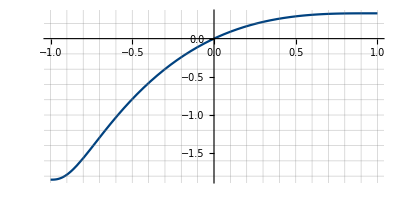

```mathematica
Plot[{
Integrate[(1-x^10)^2(1-x)^2,x]//Evaluate
},{x,-1,1},PlotRange->Full,AspectRatio->1/2,PlotStyle->Hue[0.58, 1, 0.5],GridLines->{Table[i,{i,-1,1,0.1}],Table[i,{i,-2,1,0.2}]}]
```

Для этого мы сначала сместим функцию наверх, чтобы выровнять левый край, а затем масштабируем к двойке по правому краю и вычтем единицу. После чего получим следующую формулу:

```mathematica
Integrate[(1-x^12)^2(1-x)^2,x]//#-(#/.x->-1)&//2#/(#/.x->1)-1&//Simplify
```

-1+(8775 (117592/61425+x-x^2+x^3/3-(2 x^13)/13+(2 x^14)/7-(2 x^15)/15+x^25/25-x^26/13+x^27/27))/9856

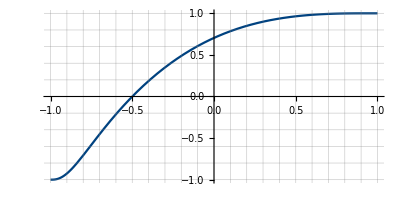

```mathematica
Plot[{
-1+1/9856 8775 (117592/61425+x-x^2+x^3/3-(2 x^13)/13+(4 x^14)/14-(2 x^15)/15+x^25/25-(2 x^26)/26+x^27/27)

},{x,-1,1},AspectRatio->1/2,PlotStyle->Hue[0.58, 1, 0.5],GridLines->{Table[i,{i,-1,1,0.1}],Table[i,{i,-2,1,0.2}]}]
```

```mathematica
AssymClip[x_]:=Piecewise[{{-1, x≤-1},{1, x≥1}},Integrate[(1-x^12)^2(1-x)^2,x]//#-(#/.x->-1)&//(2#)/(#/.x->1)-1&//Simplify]//Evaluate
```

```mathematica
AssymClip//Definition
```

AssymClip[x_]:=Piecewise[{{-1, x≤-1}, {1, x≥1}, {-1+(8775 (117592/61425+x-x^2+x^3/3-(2 x^13)/13+(2 x^14)/7-(2 x^15)/15+x^25/25-x^26/13+x^27/27))/9856, True}}]

Для того, чтобы итоговое окно имело желаемый вид, нужно также обеспечить достаточное большой уровень перекрытия:

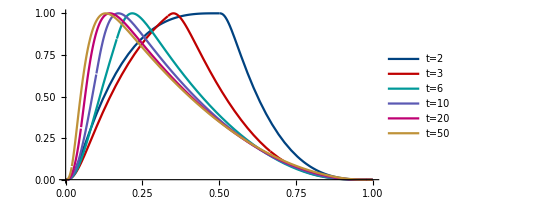

```mathematica
Plot[{
OverlapShape[AssymClip,x,2],
1.154OverlapShape[AssymClip,x,3],
2.153OverlapShape[AssymClip,x,6],
3.641OverlapShape[AssymClip,x,10],
7.49OverlapShape[AssymClip,x,20],
19.18OverlapShape[AssymClip,x,50]
},{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/20}],Table[i,{i,-1,1,1/10}]},PlotLegends->{"t=2","t=3","t=6","t=10","t=20","t=50"},Axes->{True,False},PlotStyle->{Hue[0.58, 1, 0.5],Hue[0, 1, 0.75],Hue[0.5, 1, 0.6],Hue[0.67, 0.5, 0.7],Hue[0.9, 1, 0.75],Hue[0.11, 0.7, 0.75],Hue[0.61, 1, 0.9],Hue[0.08, 1, 1],Hue[0.12, 1, 0.9]}]
```

В динамике:

```mathematica
Manipulate[Plot[
 OverlapShape[AssymClip,x,t]
,{x,0,1},PlotRange->Full,AspectRatio->1/2,GridLines->{Table[i,{i,-1,1,1/20}]},PlotStyle->Hue[0.9, 1, 0.75]]
,{{t,2.5},2,20}]
```

## Заключение

Аналогичным образом можно строить окна и из любых других колоколообразных функций - например, гауссианы; а также можно модифицировать уже рассмотренные для обеспечения большей гладкости или изменения формы кривой. 

Вне рассмотрения остался спектральный состав таких оконных функций - этому нужно посвящать отдельные исследования.

Чуть более расширенный вариант статьи (с возможностью динамического изменения параметров в рассматриваемых окнах и скрытыми формулами) в виде документа  Wolfram Mathematica можно скачать [здесь].